# Stochastic, Finite Population Simulations

Here, we consider a stochastic model of Npop individuals, one PRDM9 locus, x target loci and 2 alleles.

## Figure 7

### Importing the results from numerical simulations

#### Npop = 5000, 2 targets

```mathematica
T2N5000CO=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\PNASRevised\\RecHot_ManyTargets_FinalResults\\probCOFinal_It0_c1_f0.4_Npop5000_Nloc2_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T2N5000PRDM9=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqPRDM9Final_It0_c1_f0.4_Npop5000_Nloc2_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T2N5000Tar=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqLocMutFinal_It0_c1_f0.4_Npop5000_Nloc2_muAsym1e-07_r0.5.dat","Table"];
```

#### Npop = 5000, 10 targets

```mathematica
T10N5000CO=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\PNASRevised\\RecHot_ManyTargets_FinalResults\\probCOFinal_It0_c1_f0.4_Npop5000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T10N5000PRDM9=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqPRDM9Final_It0_c1_f0.4_Npop5000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T10N5000Tar=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqLocMutFinal_It0_c1_f0.4_Npop5000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

#### Npop = 10000, 2 targets

```mathematica
T2N10000CO=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\probCOFinal_It0_c1_f0.4_Npop10000_Nloc2_muAsym1e-07_r0.5.dat"];
```

```mathematica
T2N10000PRDM9=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqPRDM9Final_It0_c1_f0.4_Npop10000_Nloc2_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T2N10000Tar=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqLocFinal_It0_c1_f0.4_Npop10000_Nloc2_muAsym1e-07_r0.5.dat","Table"];
```

#### Npop = 10000, 10 targets

```mathematica
T10N10000CO=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\probCOFinal_It0_c1_f0.4_Npop10000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T10N10000PRDM9=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqPRDM9Final_It0_c1_f0.4_Npop10000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

```mathematica
T10N10000Tar=Import["C:\\Users\\Fred\\Dropbox\\Hotspots\\Mutation Model\\RecHot_ManyTargets_FinalResults\\freqLocMutFinal_It0_c1_f0.4_Npop10000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

### Evolution of Crossing-over rates

#### Npop = 5000, 2 targets

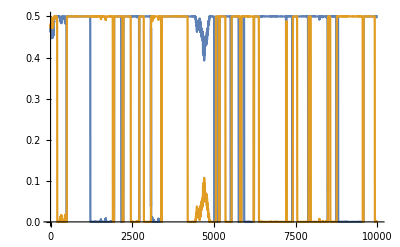

```mathematica
ListLinePlot[{(Transpose@T2N5000CO)[[1]],(Transpose@T2N5000CO)[[2]]},PlotRange->Full]
```

```mathematica
Dec={};
Dec2={};
Rec={};
Rec2={};
Per={};
For[q=1,q<Length[(Transpose@T2N5000CO)[[1]]],++q,
If[(Transpose@T2N5000CO)[[1]][[q+1]]<(Transpose@T2N5000CO)[[1]][[q]]-0.08,
AppendTo[Dec,10*q]]];
For[qq=1,qq<Length[(Transpose@T2N5000CO)[[2]]],++qq,
If[(Transpose@T2N5000CO)[[2]][[qq+1]]<(Transpose@T2N5000CO)[[2]][[qq]]-0.08,
AppendTo[Dec2,10*qq]]];
For[w=1,w<Length[Dec],++w,
If[Dec[[w+1]]-Dec[[w]]<100,AppendTo[Rec,{w+1}]]];
For[ww=1,ww<Length[Dec2],++ww,
If[Dec2[[ww+1]]-Dec2[[ww]]<100,AppendTo[Rec2,{ww+1}]]];
Dec=Delete[Dec,Rec];
Dec2=Delete[Dec2,Rec2];
For[s=2,s≤Length[Dec],++s,
AppendTo[Per,Dec[[s]]-Dec[[s-1]]]];
For[ss=2,ss≤Length[Dec2],++ss,
AppendTo[Per,Dec2[[ss]]-Dec2[[ss-1]]]];
MeanPerT2N5000=N[Mean[Per]];
VarPerT2N5000=N[StandardDeviation[Per]];
```

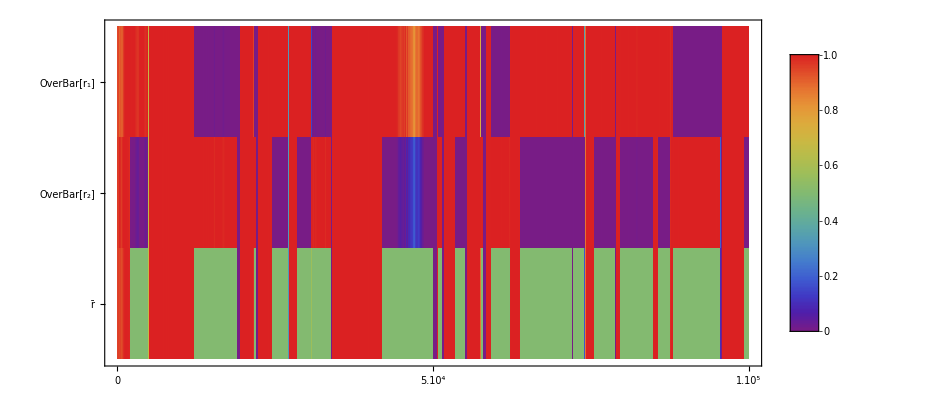

```mathematica
MM=MatrixPlot[{2*(Transpose@T2N5000CO)[[1]],2*(Transpose@T2N5000CO)[[2]],(Transpose@T2N5000CO)[[1]]+(Transpose@T2N5000CO)[[2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->20000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

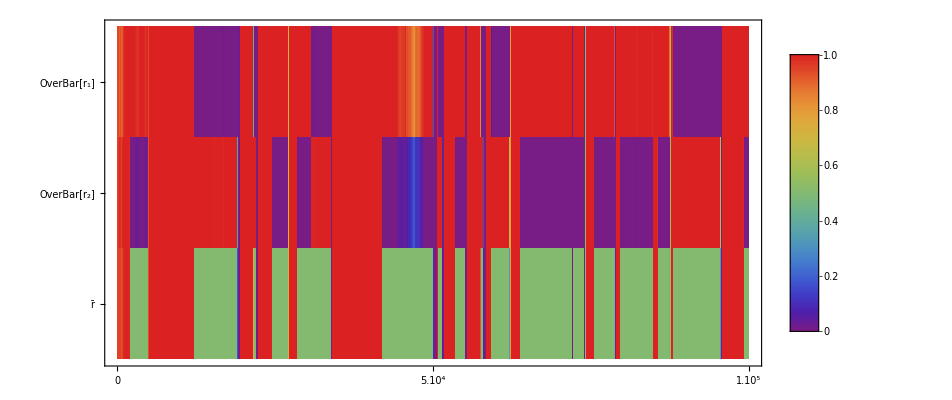

```mathematica
MM=MatrixPlot[{2*(Transpose@T2N5000CO)[[1]],2*(Transpose@T2N5000CO)[[2]],(Transpose@T2N5000CO)[[1]]+(Transpose@T2N5000CO)[[2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->2000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

#### Npop = 5000, 10 targets

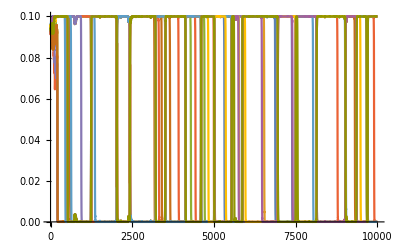

```mathematica
ListLinePlot[{(Transpose@T10N5000CO)[[1]],(Transpose@T10N5000CO)[[2]],(Transpose@T10N5000CO)[[3]],(Transpose@T10N5000CO)[[4]],(Transpose@T10N5000CO)[[5]],(Transpose@T10N5000CO)[[6]],(Transpose@T10N5000CO)[[7]],(Transpose@T10N5000CO)[[8]],(Transpose@T10N5000CO)[[9]],(Transpose@T10N5000CO)[[10]]},PlotRange->Full]
```

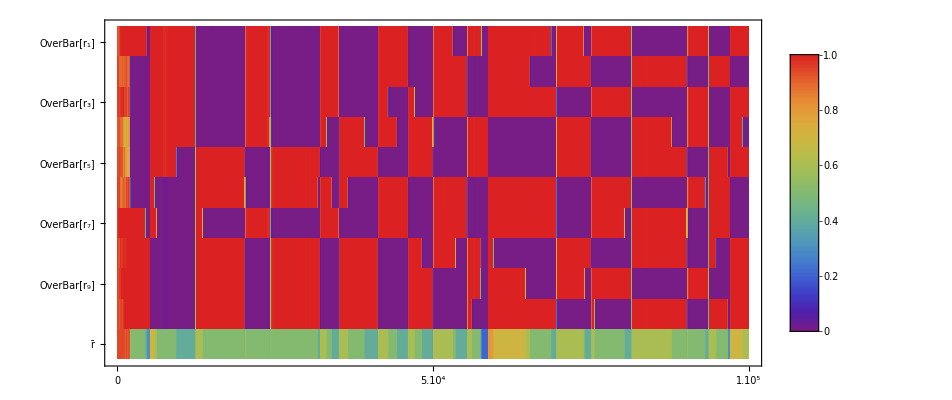

```mathematica
MM=MatrixPlot[{10*(Transpose@T10N5000CO)[[1]],10*(Transpose@T10N5000CO)[[2]],10*(Transpose@T10N5000CO)[[3]],10*(Transpose@T10N5000CO)[[4]],10*(Transpose@T10N5000CO)[[5]],10*(Transpose@T10N5000CO)[[6]],10*(Transpose@T10N5000CO)[[7]],10*(Transpose@T10N5000CO)[[8]],10*(Transpose@T10N5000CO)[[9]],10*(Transpose@T10N5000CO)[[10]],(Transpose@T10N5000CO)[[1]]+(Transpose@T10N5000CO)[[2]]+(Transpose@T10N5000CO)[[3]]+(Transpose@T10N5000CO)[[4]]+(Transpose@T10N5000CO)[[5]]+(Transpose@T10N5000CO)[[6]]+(Transpose@T10N5000CO)[[7]]+(Transpose@T10N5000CO)[[8]]+(Transpose@T10N5000CO)[[9]]+(Transpose@T10N5000CO)[[10]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->20000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"OverBar[r_3]"},{4,"OverBar[r_4]"},{5,"OverBar[r_5]"},{6,"OverBar[r_6]"},{7,"OverBar[r_7]"},{8,"OverBar[r_8]"},{9,"OverBar[r_9]"},{10,"OverBar[r_10]"},{11,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

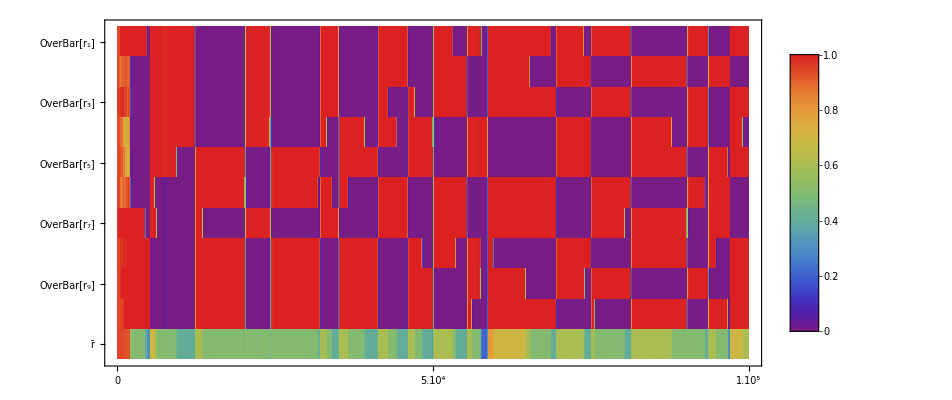

```mathematica
MM=MatrixPlot[{10*(Transpose@T10N5000CO)[[1]],10*(Transpose@T10N5000CO)[[2]],10*(Transpose@T10N5000CO)[[3]],10*(Transpose@T10N5000CO)[[4]],10*(Transpose@T10N5000CO)[[5]],10*(Transpose@T10N5000CO)[[6]],10*(Transpose@T10N5000CO)[[7]],10*(Transpose@T10N5000CO)[[8]],10*(Transpose@T10N5000CO)[[9]],10*(Transpose@T10N5000CO)[[10]],(Transpose@T10N5000CO)[[1]]+(Transpose@T10N5000CO)[[2]]+(Transpose@T10N5000CO)[[3]]+(Transpose@T10N5000CO)[[4]]+(Transpose@T10N5000CO)[[5]]+(Transpose@T10N5000CO)[[6]]+(Transpose@T10N5000CO)[[7]]+(Transpose@T10N5000CO)[[8]]+(Transpose@T10N5000CO)[[9]]+(Transpose@T10N5000CO)[[10]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->2000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"OverBar[r_3]"},{4,"OverBar[r_4]"},{5,"OverBar[r_5]"},{6,"OverBar[r_6]"},{7,"OverBar[r_7]"},{8,"OverBar[r_8]"},{9,"OverBar[r_9]"},{10,"OverBar[r_10]"},{11,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

```mathematica
Dec={};
Dec2={};
Rec={};
Rec2={};
Per={};
For[q=1,q<Length[(Transpose@T10N5000CO)[[1]]],++q,
If[(Transpose@T10N5000CO)[[1]][[q+1]]<(Transpose@T10N5000CO)[[1]][[q]]-0.008,
AppendTo[Dec,10*q]]];
For[qq=1,qq<Length[(Transpose@T10N5000CO)[[2]]],++qq,
If[(Transpose@T10N5000CO)[[2]][[qq+1]]<(Transpose@T10N5000CO)[[2]][[qq]]-0.008,
AppendTo[Dec2,10*qq]]];
For[w=1,w<Length[Dec],++w,
If[Dec[[w+1]]-Dec[[w]]<100,AppendTo[Rec,{w+1}]]];
For[ww=1,ww<Length[Dec2],++ww,
If[Dec2[[ww+1]]-Dec2[[ww]]<100,AppendTo[Rec2,{ww+1}]]];
Dec=Delete[Dec,Rec];
Dec2=Delete[Dec2,Rec2];
For[s=2,s≤Length[Dec],++s,
AppendTo[Per,Dec[[s]]-Dec[[s-1]]]];
For[ss=2,ss≤Length[Dec2],++ss,
AppendTo[Per,Dec2[[ss]]-Dec2[[ss-1]]]];
MeanPerT10N5000=N[Mean[Per]];
VarPerT10N5000=N[StandardDeviation[Per]];
```

#### Npop = 10000, 2 targets

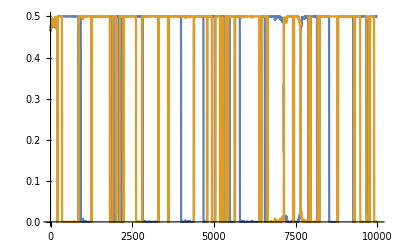

```mathematica
ListLinePlot[{(Transpose@T2N10000CO)[[1]],(Transpose@T2N10000CO)[[2]]},PlotRange->Full]
```

```mathematica
Dec={};
Dec2={};
Rec={};
Rec2={};
Per={};
For[q=1,q<Length[(Transpose@T2N10000CO)[[1]]],++q,
If[(Transpose@T2N10000CO)[[1]][[q+1]]<(Transpose@T2N10000CO)[[1]][[q]]-0.08,
AppendTo[Dec,10*q]]];
For[qq=1,qq<Length[(Transpose@T2N10000CO)[[2]]],++qq,
If[(Transpose@T2N10000CO)[[2]][[qq+1]]<(Transpose@T2N10000CO)[[2]][[qq]]-0.08,
AppendTo[Dec2,10*qq]]];
For[w=1,w<Length[Dec],++w,
If[Dec[[w+1]]-Dec[[w]]<100,AppendTo[Rec,{w+1}]]];
For[ww=1,ww<Length[Dec2],++ww,
If[Dec2[[ww+1]]-Dec2[[ww]]<100,AppendTo[Rec2,{ww+1}]]];
Dec=Delete[Dec,Rec];
Dec2=Delete[Dec2,Rec2];
For[s=2,s≤Length[Dec],++s,
AppendTo[Per,Dec[[s]]-Dec[[s-1]]]];
For[ss=2,ss≤Length[Dec2],++ss,
AppendTo[Per,Dec2[[ss]]-Dec2[[ss-1]]]];
MeanPerT2N10000=N[Mean[Per]];
VarPerT2N10000=N[StandardDeviation[Per]];
```

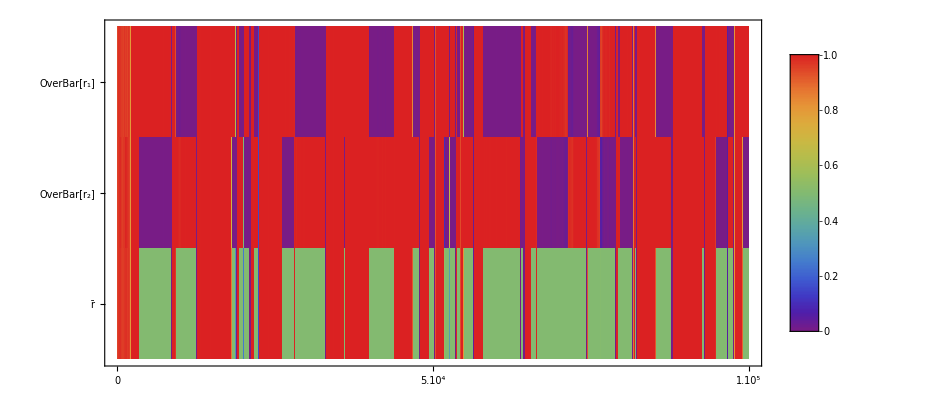

```mathematica
MM=MatrixPlot[{2*(Transpose@T2N10000CO)[[1]],2*(Transpose@T2N10000CO)[[2]],(Transpose@T2N10000CO)[[1]]+(Transpose@T2N10000CO)[[2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->20000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

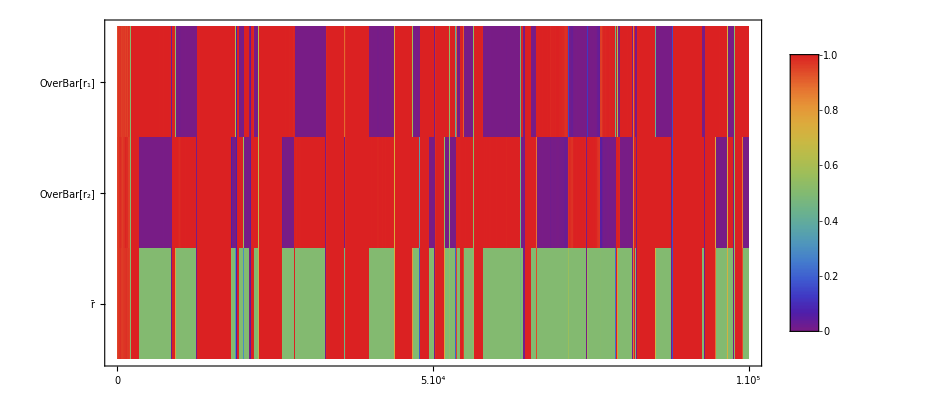

```mathematica
MM=MatrixPlot[{2*(Transpose@T2N10000CO)[[1]],2*(Transpose@T2N10000CO)[[2]],(Transpose@T2N10000CO)[[1]]+(Transpose@T2N10000CO)[[2]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->2000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

```mathematica
abc=Table[{0,0,0},{i,1,9801}];
For[i=1,i≤9801,++i,
abc[[i]][[1]]=T2N10000PRDM9[[200+i-1]][[2]];
abc[[i]][[2]]=T2N10000Tar[[200+i-1]][[2]];
abc[[i]][[3]]=T2N10000Tar[[200+i-1]][[3]]]
```

```mathematica
Buff=Table[0,{i,1,9801}];
For[j=1,j<9802,++j,
Buff[[j]]=(Transpose@T2N10000CO)[[1]][[200+(j-1)]]+(Transpose@T2N10000CO)[[2]][[200+(j-1)]]];
```

```mathematica
finter=Interpolation[#,InterpolationOrder->2,Method->"Spline"]&/@Transpose[abc];

rinter=ListInterpolation[Buff];

p1=ParametricPlot3D[Through[finter[t]],{t,1,Length[abc]},ColorFunction->Function[{x,y,z,t},ColorData["Rainbow"][rinter[t]]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Directive[Thickness[0.004],Opacity[1]],LabelStyle->Directive[ Black],Ticks->{{0,1},{0,1},{0,1}},ImageSize->{800,600},AxesLabel->{"A1","B1","C1"}]
```

-Graphics3D-

#### Npop = 10000, 10 targets

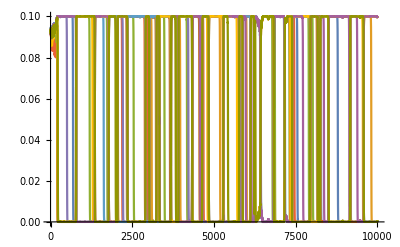

```mathematica
ListLinePlot[{(Transpose@T10N10000CO)[[1]],(Transpose@T10N10000CO)[[2]],(Transpose@T10N10000CO)[[3]],(Transpose@T10N10000CO)[[4]],(Transpose@T10N10000CO)[[5]],(Transpose@T10N10000CO)[[6]],(Transpose@T10N10000CO)[[7]],(Transpose@T10N10000CO)[[8]],(Transpose@T10N10000CO)[[9]],(Transpose@T10N10000CO)[[10]]},PlotRange->Full]
```

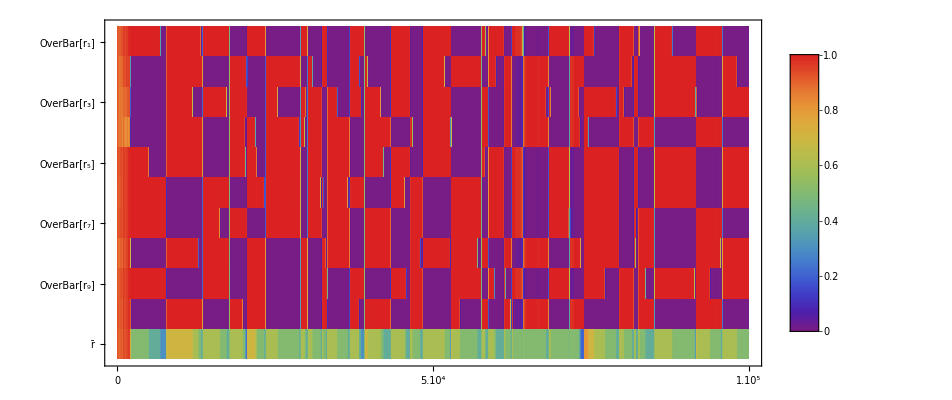

```mathematica
MM=MatrixPlot[{10*(Transpose@T10N10000CO)[[1]],10*(Transpose@T10N10000CO)[[2]],10*(Transpose@T10N10000CO)[[3]],10*(Transpose@T10N10000CO)[[4]],10*(Transpose@T10N10000CO)[[5]],10*(Transpose@T10N10000CO)[[6]],10*(Transpose@T10N10000CO)[[7]],10*(Transpose@T10N10000CO)[[8]],10*(Transpose@T10N10000CO)[[9]],10*(Transpose@T10N10000CO)[[10]],(Transpose@T10N10000CO)[[1]]+(Transpose@T10N10000CO)[[2]]+(Transpose@T10N10000CO)[[3]]+(Transpose@T10N10000CO)[[4]]+(Transpose@T10N10000CO)[[5]]+(Transpose@T10N10000CO)[[6]]+(Transpose@T10N10000CO)[[7]]+(Transpose@T10N10000CO)[[8]]+(Transpose@T10N10000CO)[[9]]+(Transpose@T10N10000CO)[[10]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->20000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"OverBar[r_3]"},{4,"OverBar[r_4]"},{5,"OverBar[r_5]"},{6,"OverBar[r_6]"},{7,"OverBar[r_7]"},{8,"OverBar[r_8]"},{9,"OverBar[r_9]"},{10,"OverBar[r_10]"},{11,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

#### Summary

```mathematica
Dec={};
Dec2={};
Rec={};
Rec2={};
Per={};
For[q=1,q<Length[(Transpose@T10N10000CO)[[1]]],++q,
If[(Transpose@T10N10000CO)[[1]][[q+1]]<(Transpose@T10N10000CO)[[1]][[q]]-0.008,
AppendTo[Dec,10*q]]];
For[qq=1,qq<Length[(Transpose@T10N10000CO)[[2]]],++qq,
If[(Transpose@T10N10000CO)[[2]][[qq+1]]<(Transpose@T10N10000CO)[[2]][[qq]]-0.008,
AppendTo[Dec2,10*qq]]];
For[w=1,w<Length[Dec],++w,
If[Dec[[w+1]]-Dec[[w]]<100,AppendTo[Rec,{w+1}]]];
For[ww=1,ww<Length[Dec2],++ww,
If[Dec2[[ww+1]]-Dec2[[ww]]<100,AppendTo[Rec2,{ww+1}]]];
Dec=Delete[Dec,Rec];
Dec2=Delete[Dec2,Rec2];
For[s=2,s≤Length[Dec],++s,
AppendTo[Per,Dec[[s]]-Dec[[s-1]]]];
For[ss=2,ss≤Length[Dec2],++ss,
AppendTo[Per,Dec2[[ss]]-Dec2[[ss-1]]]];
MeanPerT10N10000=N[Mean[Per]];
VarPerT10N10000=N[StandardDeviation[Per]];
```

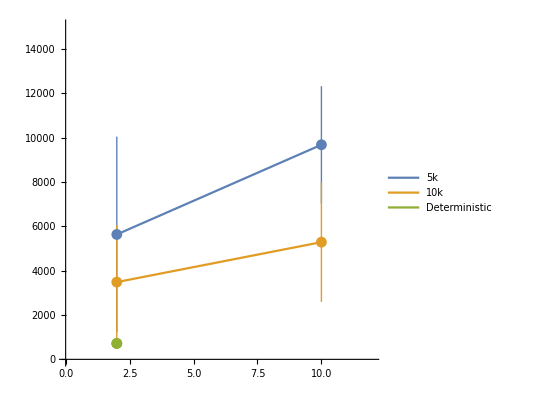

```mathematica
ListLinePlot[{{{2,Around[MeanPerT2N5000,VarPerT2N5000]},{10,Around[MeanPerT10N5000,VarPerT10N5000]}},{{2,Around[MeanPerT2N10000,VarPerT2N10000]},{10,Around[MeanPerT10N10000,VarPerT10N10000]}},{{2,717}}},Joined->True,Mesh->All,PlotLegends->{"5k","10k","Deterministic"},PlotRange->{{0,12},{0,15000}},AspectRatio->1]
```

## Figure 8

### Importing the results from numerical simulations

#### f = 0.4

```mathematica
f04=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Finite Population Stochastic Model\\ManyTarget Stochastic Model\\Results\\probCOFinal_It0_c1_f0.4_Npop10000_Nloc10_muAsym1e-07_r0.5.dat","Table"];
```

#### f = 0.3

```mathematica
f03=Import["C:\\Users\\Fred\\Dropbox\\Fyon\\RecombinationHotspost\\Project 1 - Recombination Hotspot Dynamics with Mutation\\Finite Population Stochastic Model\\ManyTarget Stochastic Model\\probCOFinal_It0_c1_f0.3_Npop10000_Nloc10_muA1e-06_muB1e-07_r0.5.dat","Table"];
```

### Heat Maps

#### f = 0.4

```mathematica
NumbCOf04=Table[0,{i,1,Length[f04]}];
For[i=1,i≤Length[f04],++i,
For[j=1,j≤10,++j,
If[f04[[i]][[j]]≥ 0.5/10,
NumbCOf04[[i]]=NumbCOf04[[i]]+1.]]]
MeanCOf04=Mean[NumbCOf04[[1000;;10000]]];
StdCOf04=StandardDeviation[NumbCOf04[[1000;;10000]]];
```

```mathematica
MeanCOf04
```

5.35952

```mathematica
StdCOf04
```

0.881073

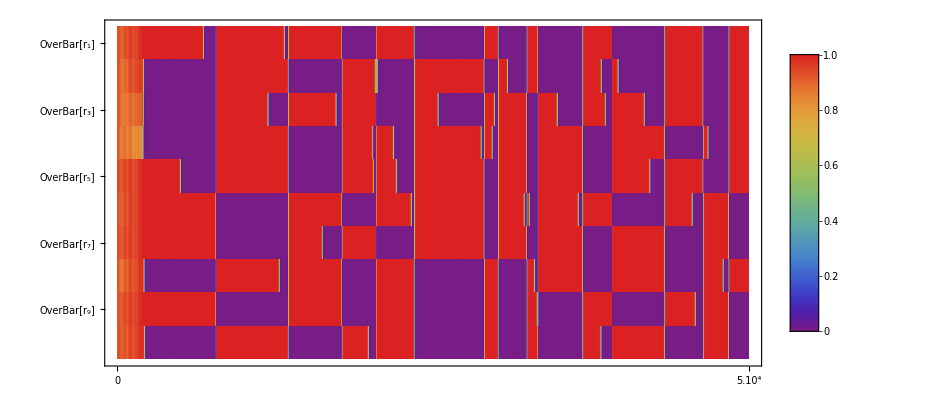

```mathematica
MM=MatrixPlot[{10*(Transpose@f04)[[1,1;;5000]],10*(Transpose@f04)[[2,1;;5000]],10*(Transpose@f04)[[3,1;;5000]],10*(Transpose@f04)[[4,1;;5000]],10*(Transpose@f04)[[5,1;;5000]],10*(Transpose@f04)[[6,1;;5000]],10*(Transpose@f04)[[7,1;;5000]],10*(Transpose@f04)[[8,1;;5000]],10*(Transpose@f04)[[9,1;;5000]],10*(Transpose@f04)[[10,1;;5000]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->5000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"OverBar[r_3]"},{4,"OverBar[r_4]"},{5,"OverBar[r_5]"},{6,"OverBar[r_6]"},{7,"OverBar[r_7]"},{8,"OverBar[r_8]"},{9,"OverBar[r_9]"},{10,"OverBar[r_10]"},{11,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```

#### f = 0.3

```mathematica
NumbCOf03=Table[0,{i,1,Length[f03]}];
For[i=1,i≤Length[f03],++i,
For[j=1,j≤10,++j,
If[f03[[i]][[j]]≥ 0.5/10,
NumbCOf03[[i]]=NumbCOf03[[i]]+1.]]]
MeanCOf03=Mean[NumbCOf03[[1000;;10000]]];
StdCOf03=StandardDeviation[NumbCOf03[[1000;;10000]]];
```

```mathematica
MeanCOf03
```

5.41651

```mathematica
StdCOf03
```

1.29561

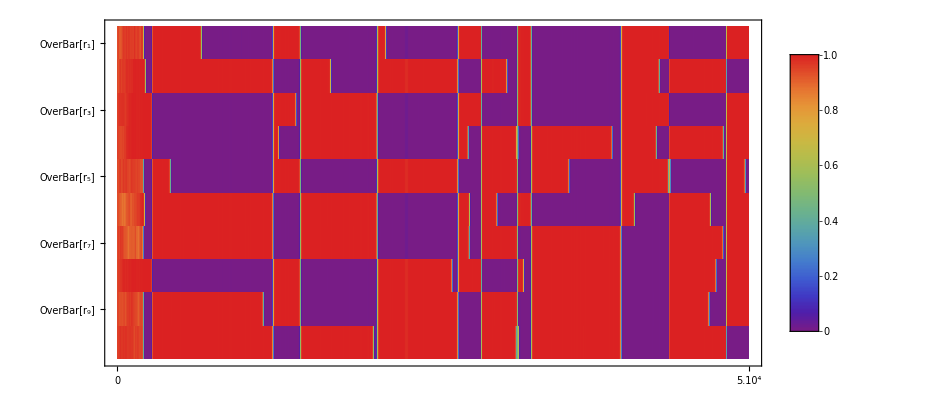

```mathematica
MM=MatrixPlot[{10*(Transpose@f03)[[1,1;;5000]],10*(Transpose@f03)[[2,1;;5000]],10*(Transpose@f03)[[3,1;;5000]],10*(Transpose@f03)[[4,1;;5000]],10*(Transpose@f03)[[5,1;;5000]],10*(Transpose@f03)[[6,1;;5000]],10*(Transpose@f03)[[7,1;;5000]],10*(Transpose@f03)[[8,1;;5000]],10*(Transpose@f03)[[9,1;;5000]],10*(Transpose@f03)[[10,1;;5000]]},ColorFunction->ColorData["Rainbow"],ColorFunctionScaling->False,MaxPlotPoints->5000,AspectRatio->1/2,ImageSize->{800,800},Frame->True,FrameStyle->Thick,FrameTicks->{{{1,"OverBar[r_1]"},{2,"OverBar[r_2]"},{3,"OverBar[r_3]"},{4,"OverBar[r_4]"},{5,"OverBar[r_5]"},{6,"OverBar[r_6]"},{7,"OverBar[r_7]"},{8,"OverBar[r_8]"},{9,"OverBar[r_9]"},{10,"OverBar[r_10]"},{11,"r̄"}},{0,{5000,"5.10^4"},{10000,"1.10^5"}}},FrameTicksStyle->Directive[Black,Bold,16,Opacity[0],FontOpacity->1],PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LabelStyle->Directive[Bold,12,Black],LegendMarkerSize->400],Right]]
```